```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-10,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

## PDF

```mathematica
(*W/mu pdf*)NLLfWL= (0.002705634032562221*(-1 + x^(-1)))/
     (1 - 0.017135682206227396*(4.512918922923938 - Log[Q]));
(*γ/mu pdf*)NLLfP[x_, Q_] := ((5144.959772459887 + 41.706746184531845*Log[Q] - 
       1.*Log[Q]^2)*((0.23286810520409482*(-0.05019647001236063 + 
          0.050820821453427104/x + 0.025254322866446938*x + 
          0.0006243514410664896*Log[x] - 0.0003121757205332448*x*Log[x] + 
          Log[Q]*(4.475282434709431*^-6 - 1.1188206086773578*^-6*x + 
            (4.475282434709431*^-6 - 2.2376412173547157*^-6*x)*Log[x]) + 
          Log[Q]^3*(2.9954249057675606*^-8 - 7.488562264418902*^-9*x + 
            (2.9954249057675606*^-8 - 1.4977124528837803*^-8*x)*Log[x]) + 
          Log[Q]^5*(2.851344447543248*^-12 - 7.12836111885812*^-13*x + 
            (2.851344447543248*^-12 - 1.425672223771624*^-12*x)*Log[x]) + 
          Log[Q]^7*(6.426035213686277*^-17 - 1.606508803421569*^-17*x + 
            (6.426035213686277*^-17 - 3.213017606843138*^-17*x)*Log[x]) + 
          Log[Q]^9*(8.97112165143488*^-22 - 2.24278041285872*^-22*x + 
            (8.97112165143488*^-22 - 4.48556082571744*^-22*x)*Log[x]) + 
          Log[Q]^10*(-3.498957749738689*^-24 + 8.747394374346723*^-25*x + 
            (-3.498957749738689*^-24 + 1.7494788748693445*^-24*x)*Log[x]) + 
          Log[Q]^8*(-2.321932626668352*^-19 + 5.80483156667088*^-20*x + 
            (-2.321932626668352*^-19 + 1.160966313334176*^-19*x)*Log[x]) + 
          Log[Q]^6*(-1.4158707268552207*^-14 + 3.539676817138052*^-15*x + 
            (-1.4158707268552207*^-14 + 7.079353634276104*^-15*x)*Log[x]) + 
          Log[Q]^4*(-2.9287822611284457*^-10 + 7.321955652821114*^-11*x + 
            (-2.9287822611284457*^-10 + 1.4643911305642229*^-10*x)*Log[x]) + 
          Log[Q]^2*(-6.873099902738211*^-7 + 1.7182749756845527*^-7*x + 
            (-6.873099902738211*^-7 + 3.4365499513691054*^-7*x)*Log[x]) + 
          ArcSin[0.2791683015027376 - 0.013387201210449512*Log[Q]]*
           (0.10568504203410027 - 0.10748615458500281/x - 0.05329279915477576*
             x + (-0.0018011125509025418 + 0.0009005562754512709*x)*Log[x])))/
        (Sqrt[1.0495714523398239 - 0.010984343655725643*Log[Q]]*
         Sqrt[0.9226680555143054 + 0.017135682206227396*Log[Q]]) + 
       (38.78446808702186 - 38.08481866056622*x + 19.217321686897016*x^2 + 
         Log[Q]^2*(-0.00048717779001536285 + 0.0007111582475538456*x - 
           0.00029958400939230213*x^2 + (0.00022398045753848278 - 
             0.00011199022876924139*x)*x*Log[x]) + 
         Log[Q]^3*(-5.142211286111232*^-6 + 5.584712888909655*^-6*x - 
           2.681731043755221*^-6*x^2 + (4.4250160279842256*^-7 - 
             2.2125080139921128*^-7*x)*x*Log[x]) + 
         Log[Q]^4*(-5.419872217505981*^-8 + 7.87026168868856*^-8*x - 
           3.3225334765486354*^-8*x^2 + (2.4503894711825804*^-8 - 
             1.2251947355912902*^-8*x)*x*Log[x]) + 
         Log[Q]^5*(-3.344668177706287*^-10 + 3.8333474581551137*^-10*x - 
           1.7945039089653502*^-10*x^2 + (4.886792804488264*^-11 - 
             2.443396402244132*^-11*x)*x*Log[x]) + 
         Log[Q]^6*(-1.8999287874589977*^-12 + 2.7181824238417466*^-12*x - 
           1.154527802825186*^-12*x^2 + (8.182536363827488*^-13 - 
             4.091268181913744*^-13*x)*x*Log[x]) + 
         Log[Q]^7*(-7.226031665564217*^-15 + 9.353657170489722*^-15*x - 
           4.144922209013484*^-15*x^2 + (2.1276255049255077*^-15 - 
             1.0638127524627539*^-15*x)*x*Log[x]) + 
         Log[Q]^8*(-2.5026152954488565*^-17 + 3.914664312719544*^-17*x - 
           1.6043199020421002*^-17*x^2 + (1.4120490172706877*^-17 - 
             7.060245086353439*^-18*x)*x*Log[x]) + 
         Log[Q]^9*(-5.3092658060748197*^-20 + 7.765958554179628*^-20*x - 
           3.268806090063612*^-20*x^2 + (2.4566927481048075*^-20 - 
             1.2283463740524037*^-20*x)*x*Log[x]) + 
         Log[Q]^10*(-9.450535155605765*^-23 + 2.042356101538346*^-22*x - 
           7.468524042747305*^-23*x^2 + (1.0973025859777693*^-22 - 
             5.486512929888847*^-23*x)*x*Log[x]) + 
         Log[Q]*(0.004732014818197644 - 0.00678978213808091*x + 
           0.0028804492390696384*x^2 + (-0.002057767319883267 + 
             0.0010288836599416334*x)*x*Log[x]) - 8.462148404533865*
          Log[95.55158553262575 - 1.*Log[Q]] + 8.309292186229362*x*
          Log[95.55158553262575 - 1.*Log[Q]] - 4.192860147690808*x^2*
          Log[95.55158553262575 - 1.*Log[Q]] + x*Log[x]*(0.6996494264556375 - 
           0.3498247132278188*x + (-0.15285621830450422 + 0.07642810915225211*
              x)*Log[95.55158553262575 - 1.*Log[Q]]))/
        (x*(53.844839348093906 + 1.*Log[Q])) + 
       (7.366749791287788 - 7.238005078110058*x + 3.630353977564782*x^2 - 
         0.004975460247087688*x^3 + Log[Q]*(-0.01520861441824085 + 
           0.012814988333349368*x + 0.002607091444386756*x^2 + 
           0.002295639912187298*x^3 + (-0.006886919736561894 - 
             0.005263175975125601*x - 0.00769879161728004*x^2)*Log[x]) + 
         Log[Q]^3*(-0.00003372973915435118 + 0.00002790804568082276*x + 
           5.910294577447357*^-6*x^2 + 5.091281381788857*^-6*x^3 + 
           (-0.00001527384414536657 - 0.000012185795200764483*x - 
             0.000016817868617667616*x^2)*Log[x]) + 
         Log[Q]^5*(-4.9181497712557834*^-9 + 4.0546237841855505*^-9*x + 
           8.654484476881328*^-10*x^2 + 7.423622296235143*^-10*x^3 + 
           (-2.227086688870543*^-9 - 1.791478774099625*^-9*x - 
             2.4448906462560015*^-9*x^2)*Log[x]) + 
         Log[Q]^7*(-2.402984485659825*^-13 + 1.9792109522451844*^-13*x + 
           4.2331869278042974*^-14*x^2 + 3.6271463934487924*^-14*x^3 + 
           (-1.0881439180346378*^-13 - 8.771668325957404*^-14*x - 
             1.1936324607540866*^-13*x^2)*Log[x]) + 
         Log[Q]^9*(-3.815195777894898*^-18 + 3.143089381092421*^-18*x + 
           6.71920381186738*^-19*x^2 + 5.758786079841355*^-19*x^3 + 
           (-1.7276358239524067*^-18 - 1.391954656782646*^-18*x - 
             1.895476407537287*^-18*x^2)*Log[x]) + 
         Log[Q]^10*(8.787110812382867*^-21 - 7.28023286462473*^-21*x - 
           1.5372812923485924*^-21*x^2 - 1.3263563490389234*^-21*x^3 + 
           (3.97906904711677*^-21 + 3.1648233840567907*^-21*x + 
             4.386191878646761*^-21*x^2)*Log[x]) + 
         Log[Q]^8*(1.1887609998055912*^-15 - 9.806412905604563*^-16*x - 
           2.09036097096928*^-16*x^2 - 1.7943562261216474*^-16*x^3 + 
           (5.383068678364943*^-16 + 4.324142375103411*^-16*x + 
             5.912531829995708*^-16*x^2)*Log[x]) + 
         Log[Q]^6*(4.058384080623049*^-11 - 3.3492460420528766*^-11*x - 
           7.132975014229454*^-12*x^2 - 6.1258627632046*^-12*x^3 + 
           (1.8377588289613806*^-11 + 1.4748708839707463*^-11*x + 
             2.019202801456697*^-11*x^2)*Log[x]) + 
         Log[Q]^4*(5.01537613490749*^-7 - 4.154539349769795*^-7*x - 
           8.776173650457909*^-8*x^2 - 7.570379071558478*^-8*x^3 + 
           (2.2711137214675434*^-7 + 1.8071341690825054*^-7*x + 
             2.503103497660062*^-7*x^2)*Log[x]) + 
         Log[Q]^2*(0.0018939900281309215 - 0.0015927002432837133*x - 
           0.00032547207256871643*x^2 - 0.00028588528726504486*x^3 + 
           (0.0008576558617951345 + 0.0006586463939285154*x + 
             0.0009571605957284441*x^2)*Log[x]) - 1.8244198122681228*
          Log[53.844839348093906 + 1.*Log[Q]] + 1.7938485686072219*x*
          Log[53.844839348093906 + 1.*Log[Q]] - 0.9045670952188362*x^2*
          Log[53.844839348093906 + 1.*Log[Q]] + 
         Log[x]*(0.014926380741263066 + 0.13496403848658955*x - 
           0.045092448131400176*x^2 + (-0.030571243660900846 + 
             0.015285621830450423*x)*x*Log[53.844839348093906 + 1.*Log[Q]]))/
        (x*(-95.55158553262575 + 1.*Log[Q]))))/(3004.616892506538 - 
      13.37907862329957*Log[Q]);
```

```mathematica
$Assumptions={s>10^5,x1>0.001,x1<1,s<10^8, t<0,θ∈Reals, θw∈Reals};
```

```mathematica
integral1=Integrate[photonpdf*photonpdf2*1/x,{x,10^-8*s,1}]//Simplify
```

## numerical computation

```mathematica
(*photonpdf=NLLfP[x,10^3/2]//Simplify;
photonpdf2=NLLfP[0.01/x,10^3/2]*)
ma=1000;
Integrate[NLLfP[x,ma/2]*NLLfP[(10^-8*ma^2)/x,ma/2]*1/x,{x,0.01,1}]
```

```mathematica
shat={10^4,3*10^4,5*10^4,8*10^4,10^5,3*10^5,5*10^5,8*10^5,10^6,1.5*10^6,2.5*10^6,3.5*10^6,4.5*10^6,5.5*10^6,6.5*10^6,7.5*10^6,8.5*10^6,9.5*10^6,1.5*10^7,2.5*10^7,3.5*10^7,4.5*10^7,5.5*10^7,6.5*10^7,7.5*10^7,8.5*10^7,9.5*10^7};
partonlumiaalist=Table[Integrate[NLLfP[x,Sqrt[shat[[i]]]/2]*NLLfP[(10^-8*shat[[i]])/x,Sqrt[shat[[i]]]/2]*1/x,{x,shat[[i]]/10^8,1}],{i,1,Length[shat]}];
partonlumiaadata=Table[{shat[[i]]/10^8,partonlumiaalist[[i]]},{i,1,Length[shat]}];
```

```mathematica
partonlumiaadata[[9]]
```

{1/100,0.487777}

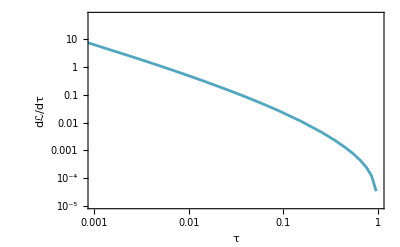

```mathematica
ListLogLogPlot[partonlumiaadata,Joined->True,PlotRange->{{10^-3,10^0},Automatic},PlotStyle->{ColorData[24][5](*,Dashed*),Thickness[0.005]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["τ",Black,15,FontFamily->"Times"],Style["dℒ/dτ",Black,15,FontFamily->"Times"]},ImageSize->400]
```

```mathematica
1/(8Pi)*((1/137)/1000)^2*ma^2*0.488*10^-8*0.389379*10^9(*change GeV^-2 to pb*)
```

4.0282×10^-6

```mathematica
1/(8Pi)*((1/137)/1000)^2*ma^2*10^-8//N
```

2.11992×10^-14

```mathematica
(4*Pi^2)/1000* 1/2*1/128^2*2^2*1000^3/(128*Pi^3*1000^2)*1/(10000)^2*0.389379*10^9(*change GeV^-2 to pb*)//N
```

4.72806×10^-6

```mathematica
0.488*(1000*0.0145)/10000^2*2
```

1.4152×10^-7

```mathematica
8*1/2*(0.118)^2*1000^3/(128*Pi^3*1000^2)
```

0.0140334